```mathematica
u=Exp[-3(xh-2)^2]
```

ⅇ^(-3 (-2+xh)^2)

```mathematica
D[u,{xh,2}]/(√π √(x-xh))//FullSimplify
```

(6 ⅇ^(-3 (-2+xh)^2) (23+6 (-4+xh) xh))/(√π √(x-xh))

```mathematica
Plot[(6 ⅇ^(-3 (-2+xh)^2) (23+6 (-4+xh) xh))/(√π √(x-xh))/.{x->-10},{xh,0,-10},PlotRange->Full]
```

-Graphics-

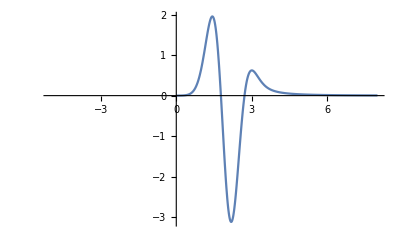

```mathematica
Plot[NIntegrate[D[u,{xh,2}]/(√π √(x-xh)),{xh,0,x}],{x,-5,8},PlotRange->Full]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

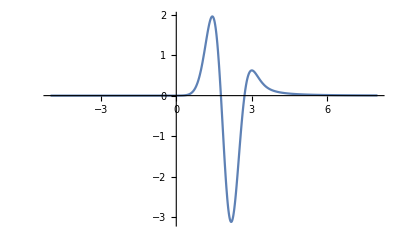

```mathematica
Plot[NIntegrate[Re[D[u,{xh,2}]/(√π √(x-xh))],{xh,0,x}],{x,-5,8},PlotRange->Full]
```

```mathematica
uExact=1/2(E^(2 π^(3/2)t)Sin[2π x-2 π^(3/2)t]+E^(-2 π^(3/2)t)Sin[2π x+2 π^(3/2)t])
```

1/2 (-ⅇ^(2 π^(3/2) t) Sin[2 π^(3/2) t-2 π x]+ⅇ^(-2 π^(3/2) t) Sin[2 π^(3/2) t+2 π x])

```mathematica
uExact/.{t->0}
```

Sin[2 π x]

```mathematica
uExact//FullSimplify
```

1/2 ⅇ^(-2 π^(3/2) t) (Sin[2 π (√π t+x)]-ⅇ^(4 π^(3/2) t) Sin[2 π^(3/2) t-2 π x])

```mathematica
uExact/.{t->3/10}//FullSimplify
```

```mathematica
D[uExact,t]//FullSimplify
```

ⅇ^(-2 π^(3/2) t) π^(3/2) (Cos[2 π (√π t+x)]-Sin[2 π (√π t+x)]-ⅇ^(4 π^(3/2) t) (Cos[2 π^(3/2) t-2 π x]+Sin[2 π^(3/2) t-2 π x]))